## Load chain

The example is analysis on the Planck chains (Planck+WP). Those chains can be downloaded at 
http://pla.esac.esa.int/pla/aio/product-action?COSMOLOGY.FILE_ID=COM_CosmoParams_base_planck_lowl_lowLike_R1.10.tar.gz
Somehow

```mathematica
<<ChainStat.m
```

LoadChain returns the whole chain, and at the same time set $Chain to the same return value.

```mathematica
LoadChain["/home/wangyi/Dropbox/a1_work/Planck_Chains/Planck_WP/base_planck_lowl_lowLike"];
```

The parameter names can be found in base_planck _lowl _lowLike.paramnames, which are (name and TEX name)

```mathematica
Transpose@Most@$Chain//MatrixForm
```

(omegabh2 | \Omega_b h^2
omegach2 | \Omega_c h^2
theta | 100\theta_{MC}
tau | \tau
ns | n_s
logA | {\rm{ln}}(10^{10} A_s)
aps100 | A^{PS}_{100}
aps143 | A^{PS}_{143}
aps217 | A^{PS}_{217}
acib143 | A^{CIB}_{143}
acib217 | A^{CIB}_{217}
asz143 | A^{tSZ}_{143}
psr | r^{PS}_{143\times217}
cibr | r^{CIB}_{143\times217}
ncib | \gamma^{CIB}
cal0 | c_{100}
cal2 | c_{217}
xi | \xi^{tSZ-CIB}
aksz | A^{kSZ}
bm_1_1 | \beta^1_1
omegal* | \Omega_\Lambda
omegam* | \Omega_m
sigma8* | \sigma_8
zrei* | z_{re}
r10* | r_{10}
H0* | H_0
r02* | r
A* | 10^9 A_s
omegamh2* | \Omega_m h^2
omegamh3* | \Omega_m h^3
yheused* | Y_P
clamp* | 10^9 A_s e^{-2\tau}
omeganuh2* | \Omega_\nu h^2
age* | {\rm{Age}}/{\rm{Gyr}}
zstar* | z_*
rstar* | r_*
thetastar* | \theta_*
zdrag* | z_{\rm{drag}}
rdrag* | r_{\rm{drag}}
kd* | k_D
thetad* | \theta_D
zeq* | z_{\rm{eq}}
thetaeq* | \theta_{\rm{eq}}
rsDv057* | r_{\rm{drag}}/D_V(0.57)
H057* | H(0.57)
DA057* | D_A(0.57))

## Select columns from chain

Columns can be selected and returned in nested list form:

```mathematica
joint=Sel[{"omegabh2","omegach2"}];
```

```mathematica
Length@joint
```

124311

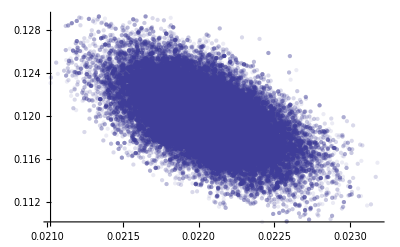

```mathematica
ListPlot[joint,PlotStyle->Opacity@0.1,PlotRange->All]
```

The joint plot using points is automated as

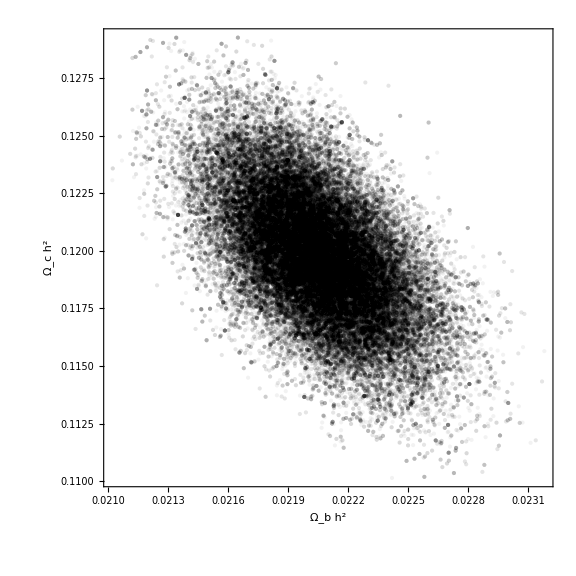

```mathematica
PtPlot[{"omegabh2","omegach2"}]
```

The -log(likelihood) = χ^2/2 can be selected using string “likelihood”.

```mathematica
2*Min[Sel["likelihood"]] (* This is the least χ^2 point in the Planck chain. Note that by minimizing χ^2 near this point in cosmomc, one can still get slightly lower χ^2. *)
```

9807.85

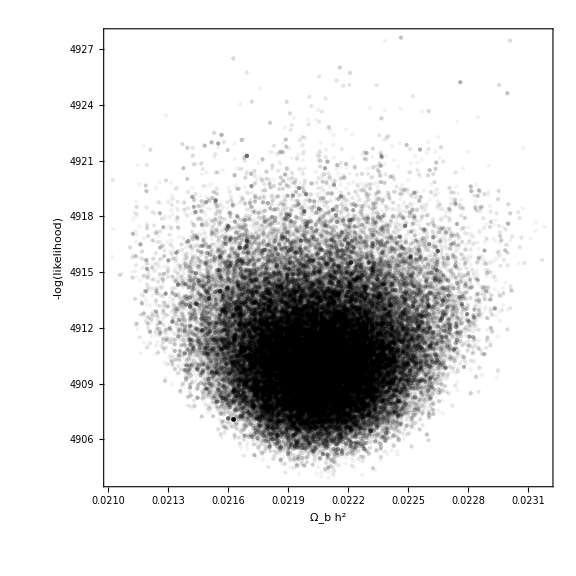

```mathematica
PtPlot[{"omegabh2","likelihood"}]
```

The selection can be supplied with conditions

```mathematica
jointCut=Sel[{"omegabh2","omegach2"},"omegach2"<0.115||"omegach2">0.12];
```

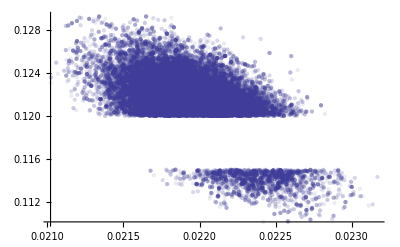

```mathematica
ListPlot[jointCut,PlotStyle->Opacity@0.1,PlotRange->All]
```

See how unprobable is “omegach2”<0.115

```mathematica
(Sel[{"omegach2"},"omegach2"<0.115]//Length)/(Sel[{"omegach2"}]//Length)//N
```

0.0329898

## Statistics plots

1d plot

Ω_c h^2 = 0.119838 ± 0.00268264 (mean, std var)

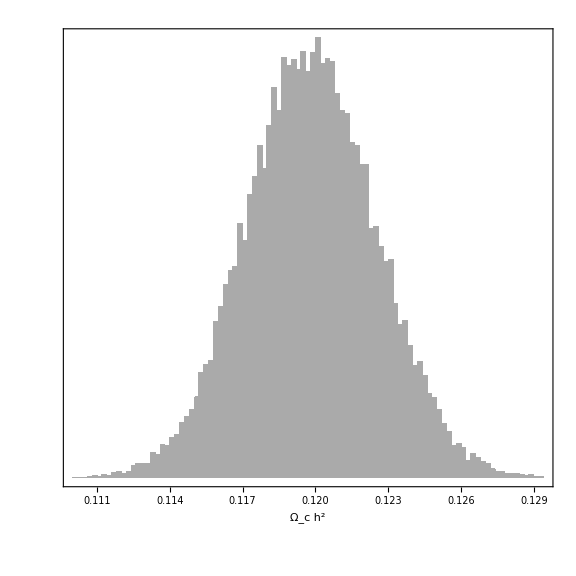

```mathematica
Stat["omegach2"]
```

2d plot

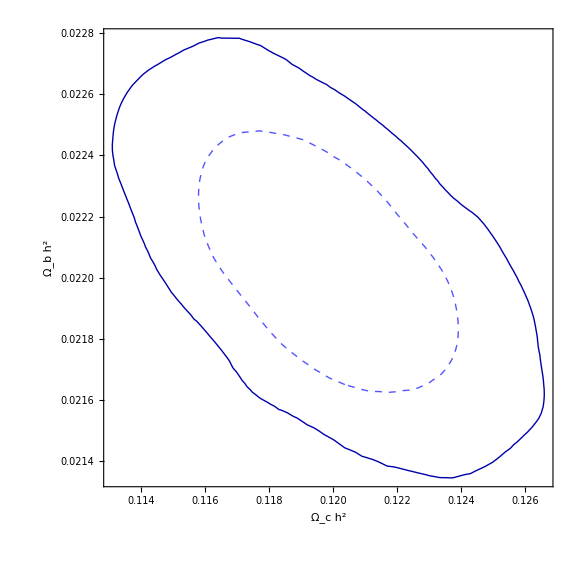

```mathematica
Stat[{"omegach2","omegabh2"}]
```

If colored contours are preferred:

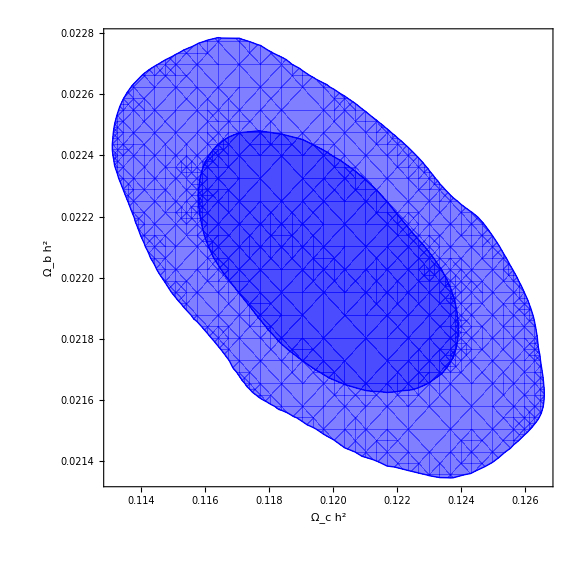

```mathematica
Stat[{"omegach2","omegabh2"},ContourShading->{None,Directive[Opacity@0.5,Blue], Directive[Opacity@0.7,Blue]},ContourStyle->Blue]
```

## Alternative chains

ChainStat using a global variable $Chain to store the chain to work on. Multiple sets of chains which can be combined can be loaded using LoadChain[{prefix1, prefix2, ...}]. 
On the other hand, if one wants to work on a completely different chain, one can use

Block[{$Chain=LoadChain[...], operations]

## Add derived parameters to chain

```mathematica
AddToChain["A", "P_\\zeta", 10^-10 Exp["logA"]];
```

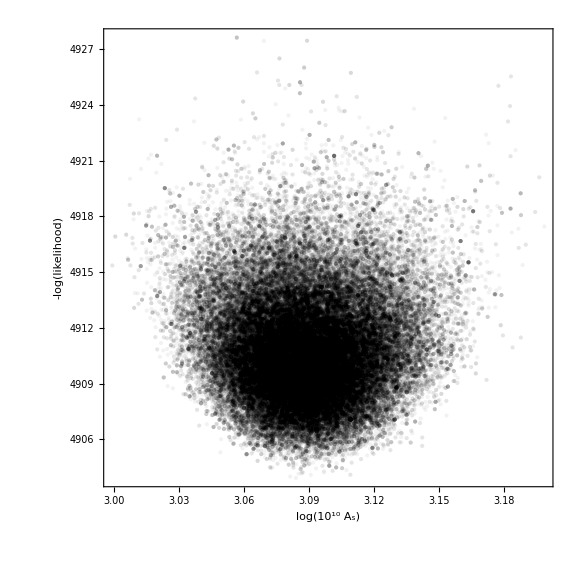

```mathematica
PtPlot[{"logA", "likelihood"}]
```

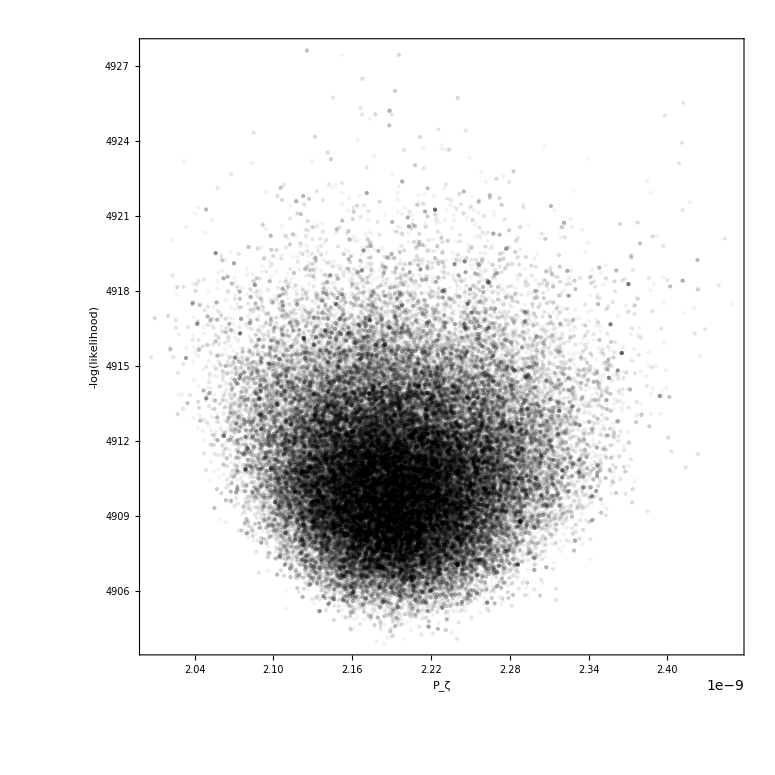

```mathematica
PtPlot[{"A", "likelihood"}]
```